EXERCISE NUMBER 1 :
write a small function that multiply a letter from the alphabet by the square root of the population of england.

WolframAlphaQueryParseResults

55268100 people

```mathematica
FullForm[Out[3]]
```

List[List[1],List[1,1],List[1,2,1],List[1,3,3,1],List[1,4,6,4,1],List[1,5,10,10,5,1],List[1,6,15,20,15,6,1],List[1,7,21,35,35,21,7,1],List[1,8,28,56,70,56,28,8,1]]

```mathematica
Quantity[55268100,"People"]
```

55268100 people

```mathematica
Out[3][[1]]
```

{1}

```mathematica
UKpopulationSqr=Sqrt[Out[3][[1]]]
```

{1}

```mathematica
myUKpopulationFunction[myletterFromAlphabet_]:=UKpopulationSqr*myLetterFromAlphabet
```

```mathematica
?myUKpopulationFunction
```

```mathematica
myUkpopulationFunction[x]
```

myUkpopulationFunction[x]

```mathematica
Function[myLetter,Function[UKpopulation,Sqrt[UKpopulation]][Out[3][[1]]]*myLetter][t]
```

{t}

Exercise2: 
Create a list made of the even numbers between 20 and 40. 
Give a name to this list.
Compute the squares(x^2)of the values (or of the list).
Store this new list into a variable.
Repeat this list 10 times.
Multiply the first list(into this new list of 10 lists) by 2, the second list by 4, the third list by 6, until the 10th list.
Then, add all the values of each list so that you will obtain a new final list with the following form(40,60,80,...120)
Finally, creates Disks whose diameter values comes from this list.
Create a GRAPHICS of these 10 disks.

```mathematica
v=Range[20,40]
```

{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
EvenQ[v]
```

{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True}

```mathematica
Select[v,EvenQ]
```

{20,22,24,26,28,30,32,34,36,38,40}

```mathematica
f=%
```

{20,22,24,26,28,30,32,34,36,38,40}

```mathematica
g= f^2
```

{400,484,576,676,784,900,1024,1156,1296,1444,1600}

```mathematica
G=ConstantArray[g,10]
```

{{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600},{400,484,576,676,784,900,1024,1156,1296,1444,1600}}

```mathematica
h=Range[1,30]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
j=Select[h,EvenQ,10]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
K=G*j
```

{{800,968,1152,1352,1568,1800,2048,2312,2592,2888,3200},{1600,1936,2304,2704,3136,3600,4096,4624,5184,5776,6400},{2400,2904,3456,4056,4704,5400,6144,6936,7776,8664,9600},{3200,3872,4608,5408,6272,7200,8192,9248,10368,11552,12800},{4000,4840,5760,6760,7840,9000,10240,11560,12960,14440,16000},{4800,5808,6912,8112,9408,10800,12288,13872,15552,17328,19200},{5600,6776,8064,9464,10976,12600,14336,16184,18144,20216,22400},{6400,7744,9216,10816,12544,14400,16384,18496,20736,23104,25600},{7200,8712,10368,12168,14112,16200,18432,20808,23328,25992,28800},{8000,9680,11520,13520,15680,18000,20480,23120,25920,28880,32000}}

```mathematica
T=Total[K]
```

{44000,53240,63360,74360,86240,99000,112640,127160,142560,158840,176000}

```mathematica
Disk[{0,0},T[[1]]]
```

Disk[{0,0},44000]



```mathematica
Graphics[Disk[{0,0},T[[1]]]]
```

```mathematica
Graphics[Disk[{0,0},T[[1]]]]
```

-Graphics-

```mathematica
Table[Graphics[{Disk[{0,0},T[[n]]]}],{n,1,11}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KK=Table[Disk[{0,0},T[[n]]],{n,1,11}]
```

{Disk[{0,0},44000],Disk[{0,0},53240],Disk[{0,0},63360],Disk[{0,0},74360],Disk[{0,0},86240],Disk[{0,0},99000],Disk[{0,0},112640],Disk[{0,0},127160],Disk[{0,0},142560],Disk[{0,0},158840],Disk[{0,0},176000]}

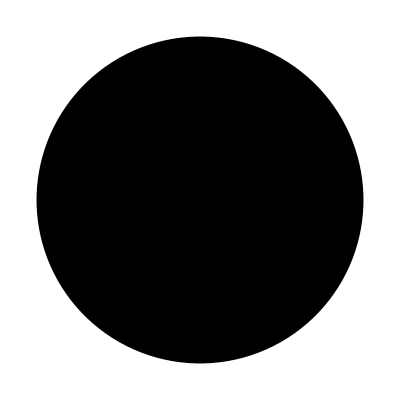

```mathematica
Graphics[KK]
```

```mathematica
MM=KK+{Red,Blue,Green,Purple,Yellow,Orange,Pink, Gray, Black,Cyan, Brown}
```

{Disk[{0,0},44000]+RGBColor[1, 0, 0],Disk[{0,0},53240]+RGBColor[0, 0, 1],Disk[{0,0},63360]+RGBColor[0, 1, 0],Disk[{0,0},74360]+RGBColor[0.5, 0, 0.5],Disk[{0,0},86240]+RGBColor[1, 1, 0],Disk[{0,0},99000]+RGBColor[1, 0.5, 0],Disk[{0,0},112640]+RGBColor[1, 0.5, 0.5],Disk[{0,0},127160]+GrayLevel[0.5],Disk[{0,0},142560]+GrayLevel[0],Disk[{0,0},158840]+RGBColor[0, 1, 1],Disk[{0,0},176000]+RGBColor[0.6, 0.4, 0.2]}

```mathematica
GG=Table[{c,Disk[{0,0},T[[n]]]},{n,1,11},{c,{Red,Blue,Green,Purple,Yellow,Orange,Pink, Gray, Black,Cyan, Brown}}]
```

{{{RGBColor[1, 0, 0],Disk[{0,0},44000]},{RGBColor[0, 0, 1],Disk[{0,0},44000]},{RGBColor[0, 1, 0],Disk[{0,0},44000]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},44000]},{RGBColor[1, 1, 0],Disk[{0,0},44000]},{RGBColor[1, 0.5, 0],Disk[{0,0},44000]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},44000]},{GrayLevel[0.5],Disk[{0,0},44000]},{GrayLevel[0],Disk[{0,0},44000]},{RGBColor[0, 1, 1],Disk[{0,0},44000]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},44000]}},{{RGBColor[1, 0, 0],Disk[{0,0},53240]},{RGBColor[0, 0, 1],Disk[{0,0},53240]},{RGBColor[0, 1, 0],Disk[{0,0},53240]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},53240]},{RGBColor[1, 1, 0],Disk[{0,0},53240]},{RGBColor[1, 0.5, 0],Disk[{0,0},53240]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},53240]},{GrayLevel[0.5],Disk[{0,0},53240]},{GrayLevel[0],Disk[{0,0},53240]},{RGBColor[0, 1, 1],Disk[{0,0},53240]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},53240]}},{{RGBColor[1, 0, 0],Disk[{0,0},63360]},{RGBColor[0, 0, 1],Disk[{0,0},63360]},{RGBColor[0, 1, 0],Disk[{0,0},63360]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},63360]},{RGBColor[1, 1, 0],Disk[{0,0},63360]},{RGBColor[1, 0.5, 0],Disk[{0,0},63360]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},63360]},{GrayLevel[0.5],Disk[{0,0},63360]},{GrayLevel[0],Disk[{0,0},63360]},{RGBColor[0, 1, 1],Disk[{0,0},63360]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},63360]}},{{RGBColor[1, 0, 0],Disk[{0,0},74360]},{RGBColor[0, 0, 1],Disk[{0,0},74360]},{RGBColor[0, 1, 0],Disk[{0,0},74360]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},74360]},{RGBColor[1, 1, 0],Disk[{0,0},74360]},{RGBColor[1, 0.5, 0],Disk[{0,0},74360]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},74360]},{GrayLevel[0.5],Disk[{0,0},74360]},{GrayLevel[0],Disk[{0,0},74360]},{RGBColor[0, 1, 1],Disk[{0,0},74360]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},74360]}},{{RGBColor[1, 0, 0],Disk[{0,0},86240]},{RGBColor[0, 0, 1],Disk[{0,0},86240]},{RGBColor[0, 1, 0],Disk[{0,0},86240]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},86240]},{RGBColor[1, 1, 0],Disk[{0,0},86240]},{RGBColor[1, 0.5, 0],Disk[{0,0},86240]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},86240]},{GrayLevel[0.5],Disk[{0,0},86240]},{GrayLevel[0],Disk[{0,0},86240]},{RGBColor[0, 1, 1],Disk[{0,0},86240]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},86240]}},{{RGBColor[1, 0, 0],Disk[{0,0},99000]},{RGBColor[0, 0, 1],Disk[{0,0},99000]},{RGBColor[0, 1, 0],Disk[{0,0},99000]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},99000]},{RGBColor[1, 1, 0],Disk[{0,0},99000]},{RGBColor[1, 0.5, 0],Disk[{0,0},99000]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},99000]},{GrayLevel[0.5],Disk[{0,0},99000]},{GrayLevel[0],Disk[{0,0},99000]},{RGBColor[0, 1, 1],Disk[{0,0},99000]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},99000]}},{{RGBColor[1, 0, 0],Disk[{0,0},112640]},{RGBColor[0, 0, 1],Disk[{0,0},112640]},{RGBColor[0, 1, 0],Disk[{0,0},112640]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},112640]},{RGBColor[1, 1, 0],Disk[{0,0},112640]},{RGBColor[1, 0.5, 0],Disk[{0,0},112640]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},112640]},{GrayLevel[0.5],Disk[{0,0},112640]},{GrayLevel[0],Disk[{0,0},112640]},{RGBColor[0, 1, 1],Disk[{0,0},112640]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},112640]}},{{RGBColor[1, 0, 0],Disk[{0,0},127160]},{RGBColor[0, 0, 1],Disk[{0,0},127160]},{RGBColor[0, 1, 0],Disk[{0,0},127160]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},127160]},{RGBColor[1, 1, 0],Disk[{0,0},127160]},{RGBColor[1, 0.5, 0],Disk[{0,0},127160]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},127160]},{GrayLevel[0.5],Disk[{0,0},127160]},{GrayLevel[0],Disk[{0,0},127160]},{RGBColor[0, 1, 1],Disk[{0,0},127160]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},127160]}},{{RGBColor[1, 0, 0],Disk[{0,0},142560]},{RGBColor[0, 0, 1],Disk[{0,0},142560]},{RGBColor[0, 1, 0],Disk[{0,0},142560]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},142560]},{RGBColor[1, 1, 0],Disk[{0,0},142560]},{RGBColor[1, 0.5, 0],Disk[{0,0},142560]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},142560]},{GrayLevel[0.5],Disk[{0,0},142560]},{GrayLevel[0],Disk[{0,0},142560]},{RGBColor[0, 1, 1],Disk[{0,0},142560]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},142560]}},{{RGBColor[1, 0, 0],Disk[{0,0},158840]},{RGBColor[0, 0, 1],Disk[{0,0},158840]},{RGBColor[0, 1, 0],Disk[{0,0},158840]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},158840]},{RGBColor[1, 1, 0],Disk[{0,0},158840]},{RGBColor[1, 0.5, 0],Disk[{0,0},158840]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},158840]},{GrayLevel[0.5],Disk[{0,0},158840]},{GrayLevel[0],Disk[{0,0},158840]},{RGBColor[0, 1, 1],Disk[{0,0},158840]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},158840]}},{{RGBColor[1, 0, 0],Disk[{0,0},176000]},{RGBColor[0, 0, 1],Disk[{0,0},176000]},{RGBColor[0, 1, 0],Disk[{0,0},176000]},{RGBColor[0.5, 0, 0.5],Disk[{0,0},176000]},{RGBColor[1, 1, 0],Disk[{0,0},176000]},{RGBColor[1, 0.5, 0],Disk[{0,0},176000]},{RGBColor[1, 0.5, 0.5],Disk[{0,0},176000]},{GrayLevel[0.5],Disk[{0,0},176000]},{GrayLevel[0],Disk[{0,0},176000]},{RGBColor[0, 1, 1],Disk[{0,0},176000]},{RGBColor[0.6, 0.4, 0.2],Disk[{0,0},176000]}}}

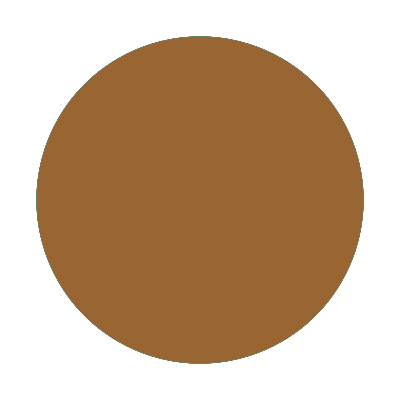

```mathematica
Graphics[GG]
```


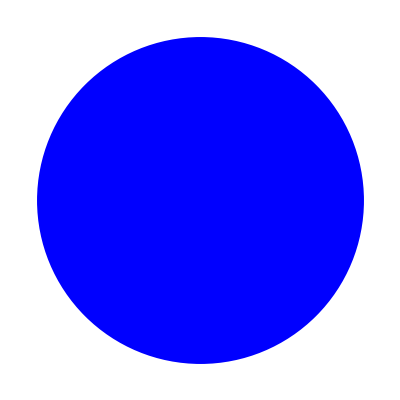
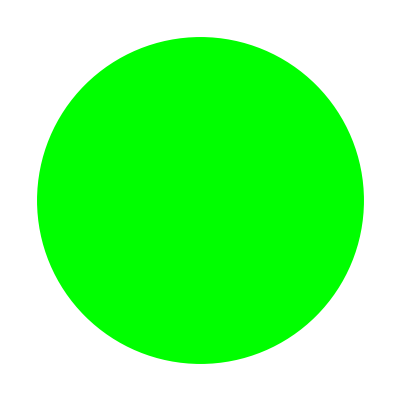
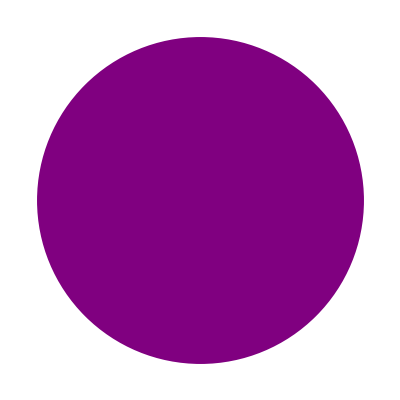
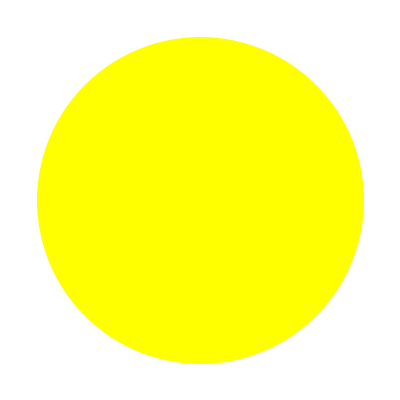
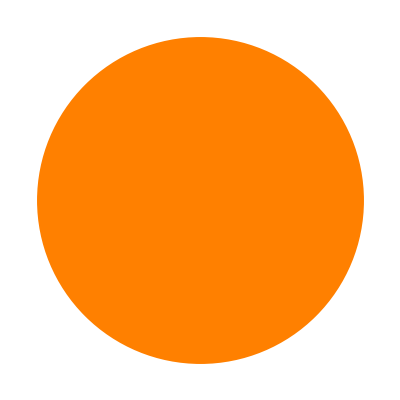
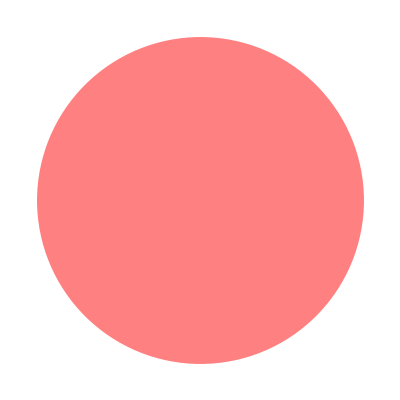
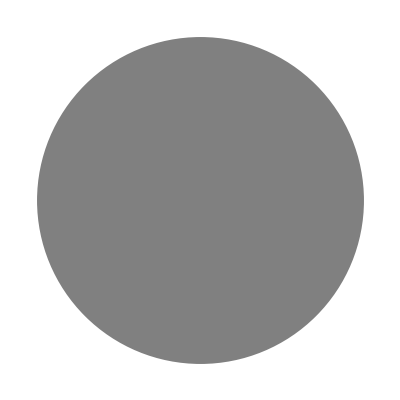
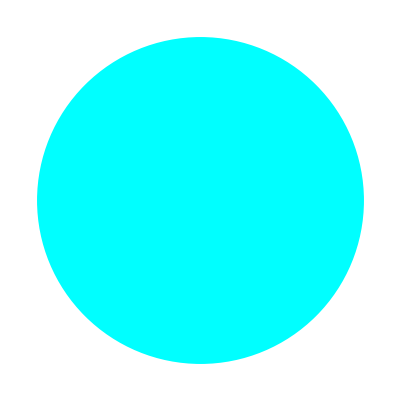
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{c,Disk[{0,0},T[[1]]]}],{c,{Red,Blue,Green,Purple,Yellow,Orange,Pink, Gray, Black,Cyan, Brown}}]
```

```mathematica
Table[Graphics[{c,Disk[{0,0},T[[n]]]}],{c,{Red,Blue,Green,Purple,Yellow,Orange,Pink, Gray, Black,Cyan, Brown}},{n,1,11}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
AA=Table[Disk[{100000n,100000n},T[[n]]],{n,1,11}]
```

{Disk[{100000,100000},44000],Disk[{200000,200000},53240],Disk[{300000,300000},63360],Disk[{400000,400000},74360],Disk[{500000,500000},86240],Disk[{600000,600000},99000],Disk[{700000,700000},112640],Disk[{800000,800000},127160],Disk[{900000,900000},142560],Disk[{1000000,1000000},158840],Disk[{1100000,1100000},176000]}

```mathematica
DD= Hue[k],Disk[{1000000n,1000000n},T[[n]],{k,0,1,0.1},{n,1,11}]??????
```

```mathematica
BB=Table[Hue[k],{k,0,1,0.1}]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.]}

```mathematica
CC=Transpose[{BB,AA}]
```

{{Hue[0.],Disk[{100000,100000},44000]},{Hue[0.1],Disk[{200000,200000},53240]},{Hue[0.2],Disk[{300000,300000},63360]},{Hue[0.30000000000000004],Disk[{400000,400000},74360]},{Hue[0.4],Disk[{500000,500000},86240]},{Hue[0.5],Disk[{600000,600000},99000]},{Hue[0.6000000000000001],Disk[{700000,700000},112640]},{Hue[0.7000000000000001],Disk[{800000,800000},127160]},{Hue[0.8],Disk[{900000,900000},142560]},{Hue[0.9],Disk[{1000000,1000000},158840]},{Hue[1.],Disk[{1100000,1100000},176000]}}

```mathematica
Graphics[CC]
```

-Graphics-

```mathematica
Graphics[{Red,Disk[{0,0},T[[1]]],Blue,Disk[{100000,100000},T[[2]]],Green,Disk[{200000,200000},T[[3]]],Purple,Disk[{300000,300000},T[[4]]],Yellow,Disk[{400000,400000},T[[5]]],Orange,Disk[{500000,500000},T[[6]]],Pink,Disk[{600000,600000},T[[7]]],Gray,Disk[{700000,700000},T[[8]]], Black,Disk[{800000,800000},T[[9]]],Cyan,Disk[{900000,900000},T[[10]]], Brown,Disk[{1000000,1000000},T[[11]]]}]
```

-Graphics-